```mathematica
(*Task0*)
```

```mathematica
cos[π/3]
(*Name of the function must start with capital letter*)

p(x_):=x^7+E^x
(*Argument of the function should be enclose by square brackets*)

(PlotE)^x
(*There is no interval for 'x'*)

ListPlot[{0,0},{1,1},{2,√2},{3,√3},{4,2},{5,√5}]
(*Arguments of function 'ListPlot' should be list of lists*)

list={1;2;3;4;8};
list[[5]]
(*Elements of list are separated with comma,not by semicolon*)
```

```mathematica
(*Task1*)
data1={{1980,338.7},{1982,341.1},{1984,344.4},{1986,347.2},{1988,351.5},{1990,354.2},{1992,356.4},{1994,358.9},{1996,362.6},{1998,366.6},{2000,369.4}};
```

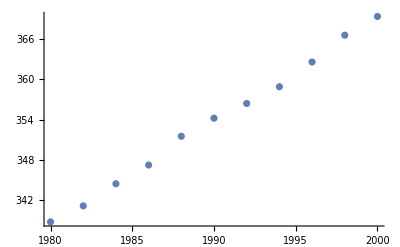

```mathematica
plot1=ListPlot[data1]
```

```mathematica
line = Fit[data1, {1,x},x]
```

-2707.25+1.53818 x

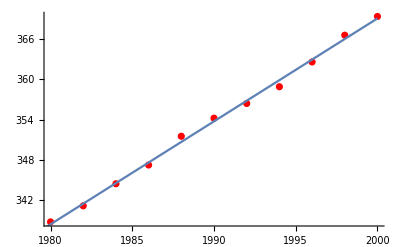

```mathematica
Show[ListPlot[data1, PlotStyle->Red], Plot[line, {x, 2000, 370}]]
```

```mathematica
(*Task2*)
Simplify[(2-√3+x) (-4+x)(2+√3+x)]
```

-4-15 x+x^3

```mathematica
q=-4;
```

```mathematica
p=-15;
```

```mathematica
x1=(-q/2+√(q^2/4+p^3/27))^(1/3)+(-q/2-√(q^2/4+p^3/27))^(1/3)
```

4

```mathematica
(*Task3*)
Refine[Log[E^x],x>0]
```

x

```mathematica
Refine[Log[E^x]==x,x>0]
```

True

```mathematica
Simplify[Log[E^x],x>0]
```

x

```mathematica
(*Task4a*)
```

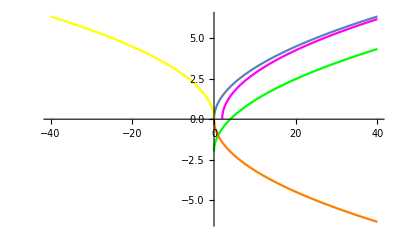

```mathematica
Show [Plot[Sqrt[x],{x,-40,40}],
Plot[Sqrt[x]-2,{x,-40,40},PlotStyle->Green],Plot[Sqrt[x-2],{x,-40,40},PlotStyle->Magenta],Plot[-Sqrt[x],{x,-40,40},PlotStyle->Orange],Plot[Sqrt[-x],{x,-40,40},PlotStyle->Yellow],PlotRange->All]
```

```mathematica
(*Task4b*)
```

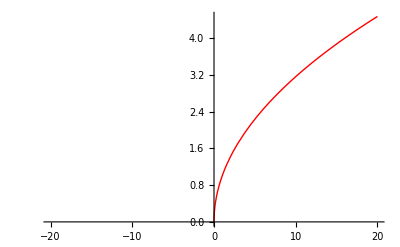

```mathematica
Plot[Sqrt[x],{x,-20,20},PlotStyle->{Red,Thick}]
```

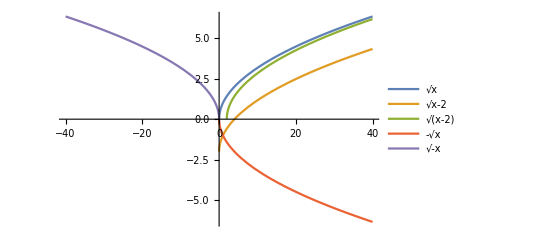

```mathematica
(*Task4c*)
Plot[{Sqrt[x],
Sqrt[x]-2,Sqrt[x-2],-Sqrt[x],Sqrt[-x]},{x,-40,40},PlotLegends->"Expressions"]
```